```mathematica
Clear[m,n]
```

```mathematica
$Assumptions={m,n}∈PositiveIntegers;
```

```mathematica
∏_(k=0)^Min[m-1,n-1] (Max[n,m]-k)
```

(Max[m,n]-Min[-1+m,-1+n]) Pochhammer[1+Max[m,n]-Min[-1+m,-1+n],Min[-1+m,-1+n]]

```mathematica
FullSimplify[%]/.{Gamma[q_]->(q-1)!}
```

(Max[m,n]!)/((-1+Max[m,n]-Min[-1+m,-1+n])!)

### Experiment

```mathematica
n=30;
m=20;
p=Range[n];
o=Range[m];
w=RandomVariate[PoissonDistribution[10],n];
pZ=RandomVariate[NormalDistribution[0,10],n];
oZ=RandomVariate[NormalDistribution[0,10],m];
dis=5Ramp[DistanceMatrix[pZ,oZ]-5];
```

```mathematica
f[{p_,o_}]:=dis[[p,o]]
Life[alloc_]:=Total[f/@alloc]
Wait[p_,alloc_]:=Total[w⟦Complement[p,RandomAlloc[p,o][[All,1]]]⟧]
Goal[p_,alloc_]:=Wait[p,alloc]+Life[alloc]
NormlizedGoal[p_,alloc_]:=Goal[p,alloc]-Total[w[[p]]]
RandomAlloc[p_,o_]:=MapIndexed[If[#2[[1]]<=w[[#1[[1]]]]&&f[#1]>w[[#2[[1]]]],#1,Nothing]&,{RandomSample[p][[;;Min[m,n]]],RandomSample[o][[;;Min[m,n]]]}ᵀ]
SampleGoal[p,o]:=NormlizedGoal[p,RandomAlloc[p,o]]
```

```mathematica
smps=Table[SampleGoal[p,o]/n,10000];
Max[smps]/Mean[smps]
```

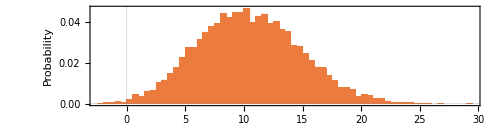

```mathematica
Histogram[smps,50,"Probability",Frame->True,FrameLabel->{"Years of Life Added Per Patient","Probability"},LabelStyle->{FontSize->18,FontColor->Black,FontFamily->"CMU Sans Serif"},PlotTheme->"Scientific",AspectRatio->1/4]
```